### Expressions

Everything in the Wolfram Language is an expression

head[arg_1,arg_2,...,arg_n]

arg_1 : head_1[arg_(1,1),arg_(1,2),...,arg_(1,n_1)]

arg_2: head_2[arg_(2,1), arg_(2,2),...,arg_(2,n_2)]

⋮

arg_n: head_2[arg_(n,1), arg_(n,2),...,arg_(n,n_n)]

#### Atomic Elements

Atomic Elements or Atomic Expressions can be though of as the basic types of elements in the Wolfram Language. They include

Integer

```mathematica
{1,2,3,4,-1,-2,-3,..}
```

Real

```mathematica
{3.4,2.,9.123456,...}
```

String

```mathematica
{"Hello","Welcome to day 2 of the Wolfram Workshop!", "xadsasvasd",...}
```

Rational

```mathematica
{1/2,3/4,4/5,16/3,...}
```

Symbol

```mathematica
{x, Pi, π, hello, Plot,...}
```

We can identify which constructs are atoms by using the AtomQ function.

```mathematica
(*Examples*){AtomQ[1],AtomQ[3.4],AtomQ["Hello"],AtomQ[1/2],AtomQ[x]}
```

{True,True,True,True,True}

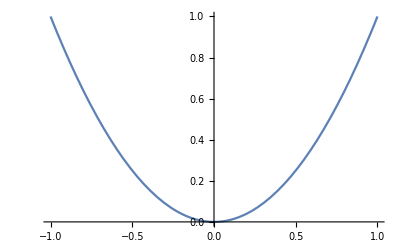
```mathematica
(*Non-Examples*){AtomQ[2x],AtomQ[5 x^2+6x+1==0],AtomQ[{1,2,3}],AtomQ[LinguisticAssistant],AtomQ[-Graphics-]}
```

{False,False,False,False,False}

This tells you that these last expressions are something more complicated (we will get to that later).

We can tell what “type” of atomic elements we have by using the Head function.

```mathematica
{Head[1],Head[3.4],Head["Hello"],Head[1/2],Head[x]}
```

{Integer,Real,String,Rational,Symbol}

#### More complex expressions

What about the non-atomic expressions that we had before?

We can still take the Head of any expression.

```mathematica
{Head[2x],Head[5 x^2+6x+1==0],Head[{1,2,3}],Head[LinguisticAssistant],Head[-Graphics-]}
```

{Times,Equal,List,Entity,Graphics}

Even though they look all different, internally they all have the same structure, that comes from language design principles in logic. That is, they all have the form:

head[argument1, argument2,...]

where the heads are Times, Equal, List, Entity, and Graphics respectively, and each argument could be either another complex expression or an atomic element.

We can see in detail how these expressions are understood by the software using the FullForm function

```mathematica
FullForm[2x]
```

Times[2,x]

```mathematica
FullForm[5 x^2+6x+1==0]
```

Equal[Plus[1,Times[6,x],Times[5,Power[x,2]]],0]

```mathematica
FullForm[{1,2,3}]
```

List[1,2,3]

```mathematica
FullForm[LinguisticAssistant]
```

Entity["Person","StephenWolfram::j276d"]

```mathematica
FullForm[-Graphics-]
```

Graphics[List[List[List[],List[],Annotation[List[RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6],Opacity[1.],Line[List[List[-1.,1.],List[-0.999387,0.998774],List[-0.998773,0.997548],List[-0.997546,0.995099],List[-0.995093,0.99021],List[-0.990186,0.980468],List[-0.980371,0.961128],List[-0.960743,0.923026],List[-0.918183,0.843061],List[-0.878444,0.771664],List[-0.839485,0.704735],List[-0.797223,0.635565],List[-0.757782,0.574233],List[-0.715038,0.51128],List[-0.673074,0.453029],List[-0.633931,0.401868],List[-0.591485,0.349855],List[-0.55186,0.304549],List[-0.513014,0.263183],List[-0.470866,0.221715],List[-0.431539,0.186226],List[-0.388909,0.15125],List[-0.347059,0.12045],List[-0.308029,0.0948819],List[-0.265697,0.0705949],List[-0.26508,0.0702672],List[-0.264462,0.0699403],List[-0.263228,0.0692888],List[-0.260758,0.0679948],List[-0.255819,0.0654434],List[-0.245941,0.0604871],List[-0.226185,0.0511599],List[-0.225516,0.0508577],List[-0.224848,0.0505564],List[-0.22351,0.0499565],List[-0.220834,0.0487675],List[-0.215482,0.0464325],List[-0.204779,0.0419343],List[-0.20411,0.0416607],List[-0.203441,0.0413881],List[-0.202103,0.0408455],List[-0.199427,0.0397711],List[-0.194075,0.0376652],List[-0.183372,0.0336252],List[-0.182715,0.0333848],List[-0.182058,0.0331452],List[-0.180745,0.0326686],List[-0.178117,0.0317258],List[-0.172863,0.0298817],List[-0.162355,0.026359],List[-0.161698,0.0261462],List[-0.161041,0.0259342],List[-0.159728,0.0255129],List[-0.1571,0.0246805],List[-0.151846,0.0230572],List[-0.141338,0.0199763],List[-0.140725,0.0198035],List[-0.140112,0.0196314],List[-0.138887,0.0192895],List[-0.136436,0.0186147],List[-0.131534,0.0173012],List[-0.121731,0.0148184],List[-0.121118,0.0146696],List[-0.120505,0.0145215],List[-0.11928,0.0142277],List[-0.116829,0.013649],List[-0.111927,0.0125277],List[-0.102124,0.0104293],List[-0.101459,0.010294],List[-0.100795,0.0101597],List[-0.0994665,0.00989358],List[-0.0968092,0.00937203],List[-0.0914948,0.00837129],List[-0.0908304,0.00825017],List[-0.0901661,0.00812993],List[-0.0888375,0.0078921],List[-0.0861803,0.00742704],List[-0.0808658,0.00653927],List[-0.0802015,0.00643227],List[-0.0795371,0.00632616],List[-0.0782085,0.00611657],List[-0.0755513,0.00570799],List[-0.0702368,0.00493321],List[-0.0596078,0.00355309],List[-0.0589875,0.00347953],List[-0.0583673,0.00340674],List[-0.0571268,0.00326347],List[-0.0546458,0.00298617],List[-0.0496839,0.00246849],List[-0.0490636,0.00240724],List[-0.0484434,0.00234676],List[-0.0472029,0.00222811],List[-0.0447219,0.00200005],List[-0.03976,0.00158086],List[-0.0391397,0.00153192],List[-0.0385195,0.00148375],List[-0.037279,0.00138972],List[-0.034798,0.0012109],List[-0.0341778,0.00116812],List[-0.0335575,0.00112611],List[-0.0323171,0.00104439],List[-0.0298361,0.000890192],List[-0.0292158,0.000853565],List[-0.0285956,0.000817708],List[-0.0273551,0.000748302],List[-0.0248741,0.000618722],List[-0.0242539,0.000588251],List[-0.0236336,0.000558549],List[-0.0223932,0.000501453],List[-0.0199122,0.000396495],List[-0.0193041,0.000372649],List[-0.0186961,0.000349542],List[-0.0174799,0.000305548],List[-0.0168719,0.00028466],List[-0.0162638,0.000264511],List[-0.0150477,0.000226432],List[-0.0144396,0.000208502],List[-0.0138315,0.000191311],List[-0.0126154,0.000159149],List[-0.0120073,0.000144176],List[-0.0113993,0.000129944],List[-0.0101832,0.000103697],List[-0.00957509,0.0000916824],List[-0.00896703,0.0000804076],List[-0.00835896,0.0000698723],List[-0.0077509,0.0000600765],List[-0.00714284,0.0000510201],List[-0.00653477,0.0000427033],List[-0.00592671,0.0000351259],List[-0.00531865,0.000028288],List[-0.00471058,0.0000221896],List[-0.00410252,0.0000168307],List[-0.00349445,0.0000122112],List[-0.00288639,8.33125×10^-6],List[-0.00227833,5.19077×10^-6],List[-0.00167026,2.78978×10^-6],List[-0.0010622,1.12826×10^-6],List[-0.000454134,2.06238×10^-7],List[0.00015393,2.36943×10^-8],List[0.000761994,5.80634×10^-7],List[0.00137006,1.87706×10^-6],List[0.00197812,3.91296×10^-6],List[0.00258619,6.68835×10^-6],List[0.00319425,0.0000102032],List[0.00380231,0.0000144576],List[0.00441038,0.0000194514],List[0.00501844,0.0000251847],List[0.0056265,0.0000316576],List[0.00623457,0.0000388698],List[0.00684263,0.0000468216],List[0.0074507,0.0000555129],List[0.00805876,0.0000649436],List[0.00927489,0.0000860235],List[0.00988295,0.0000976727],List[0.010491,0.000110061],List[0.0117071,0.000137057],List[0.0123152,0.000151664],List[0.0129233,0.000167011],List[0.0141394,0.000199923],List[0.0147475,0.000217488],List[0.0153555,0.000235792],List[0.0165717,0.00027462],List[0.0190039,0.000361149],List[0.0196636,0.000386656],List[0.0203232,0.000413034],List[0.0216425,0.0004684],List[0.0242812,0.000589576],List[0.0249408,0.000622046],List[0.0256005,0.000655386],List[0.0269198,0.000724677],List[0.0295585,0.000873703],List[0.0302181,0.000913135],List[0.0308778,0.000953437],List[0.0321971,0.00103665],List[0.0348357,0.00121353],List[0.040113,0.00160905],List[0.0407727,0.00166241],List[0.0414323,0.00171664],List[0.0427516,0.0018277],List[0.0453903,0.00206028],List[0.0506676,0.0025672],List[0.0513272,0.00263448],List[0.0519869,0.00270264],List[0.0533062,0.00284155],List[0.0559448,0.00312982],List[0.0612221,0.00374815],List[0.0618377,0.0038239],List[0.0624533,0.00390041],List[0.0636845,0.00405571],List[0.0661468,0.0043754],List[0.0710716,0.00505117],List[0.0716872,0.00513905],List[0.0723028,0.00522769],List[0.0735339,0.00540724],List[0.0759963,0.00577544],List[0.080921,0.00654821],List[0.0815366,0.00664822],List[0.0821522,0.00674899],List[0.0833834,0.00695279],List[0.0858458,0.0073695],List[0.0907705,0.00823928],List[0.10062,0.0101244],List[0.101287,0.0102591],List[0.101954,0.0103947],List[0.103289,0.0106686],List[0.105957,0.011227],List[0.111295,0.0123866],List[0.12197,0.0148767],List[0.122637,0.0150399],List[0.123304,0.015204],List[0.124639,0.0155348],List[0.127307,0.0162072],List[0.132645,0.0175947],List[0.14332,0.0205406],List[0.143975,0.0207288],List[0.14463,0.0209178],List[0.14594,0.0212985],List[0.14856,0.0220701],List[0.1538,0.0236545],List[0.16428,0.026988],List[0.18524,0.034314],List[0.185851,0.0345407],List[0.186462,0.0347682],List[0.187684,0.0352253],List[0.190128,0.0361486],List[0.195015,0.038031],List[0.20479,0.0419391],List[0.22434,0.0503287],List[0.225003,0.0506264],List[0.225666,0.0509249],List[0.226991,0.0515247],List[0.229641,0.0527349],List[0.234941,0.0551973],List[0.245542,0.0602907],List[0.266743,0.0711517],List[0.306325,0.0938348],List[0.345127,0.119113],List[0.387231,0.149948],List[0.426516,0.181916],List[0.469102,0.220056],List[0.508868,0.258946],List[0.547854,0.300144],List[0.590143,0.348268],List[0.629611,0.39641],List[0.672381,0.452096],List[0.714372,0.510327],List[0.753542,0.567826],List[0.796015,0.633639],List[0.835667,0.698339],List[0.874539,0.764819],List[0.916714,0.840365],List[0.956069,0.914067],List[0.956755,0.91538],List[0.957441,0.916694],List[0.958814,0.919325],List[0.96156,0.924598],List[0.967051,0.935189],List[0.978034,0.956551],List[0.978721,0.957894],List[0.979407,0.959238],List[0.98078,0.961929],List[0.983526,0.967323],List[0.989017,0.978155],List[0.989704,0.979513],List[0.99039,0.980872],List[0.991763,0.983594],List[0.994509,0.989047],List[0.995195,0.990413],List[0.995881,0.99178],List[0.997254,0.994516],List[0.997941,0.995886],List[0.998627,0.997256],List[0.999314,0.998628],List[1.,1.]]]],"Charting`Private`Tag$833288#1"]],List[]],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],Rule[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[ImagePadding,All],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[-1,1],List[0.,1.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[Ticks,List[Automatic,Automatic]]]

```mathematica
{InputForm[2x],InputForm[5 x^2+6x+1==0],InputForm[{1,2,3}],InputForm[LinguisticAssistant]}
```

{2*x,1 + 6*x + 5*x^2,{1, 2, 3},Entity["Person", "StephenWolfram::j276d"]}

#### An Important Observation about Head

Even though Head gives you the type of element we are working with, it should not be confused with the Function that led to its creation.

```mathematica
{Table[i,{i,5}],Range[5],List[1,2,3,4,5],Map[Length,{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}]}
```

{{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}}

```mathematica
Head/@%
```

{List,List,List,List}

Other Examples

```mathematica
Head[12+3]
```

Integer

```mathematica
Head[Sin[3]]
```

Sin

```mathematica
Head[Sin[3.]]
```

Real

#### Why is understanding expressions important

Everything is an expression

The notebook I am presenting with, the cells, and the code itself are all expressions

To understand the language and different constructs as they appear.

Knowing that there is a carefully thought structuring of the language helps you get familiar with new functionality as you run into it.

To be able to read code from others(and eventually modify it for your own purposes)

Even though there is a standard form (FullForm) of expressions there are different ways in which code can be input.

f@a

a//f

f[a]

#### Functions that work with all Expressions

Head

Head[atomic] gives you the type of atomic element.

head[f[e1,e2,...,en]] gives you f.

Length

Length of an atomic element gives you 0.

```mathematica
Length["Hello there"]
```

0

Length  of f[e1,e2,..en] gives you n.

```mathematica
Length[{1,2,3,4}]
```

4

```mathematica
Length[a+2x y]
```

2

```mathematica
Length[If[a<b,"x","y"]]
```

3

Part

Part[expr,0] is the same as taking Head[expr]

Part[f[e1,e2,...,en],k] is the same as ek.

We usually use the shorthand expr[[k]] for Part[expr,k]

```mathematica
{1,2,3,4}[[2]]
```

2

```mathematica
{1,2,3,4}[[0]]
```

List

```mathematica
3[[0]]
```

Integer

```mathematica
x[[0]]
```

Symbol

```mathematica
x[[1]]
```

Part::partd: Part specification x⟦1⟧ is longer than depth of object.

x⟦1⟧

```mathematica
{1,2,3,4}[[5]]
```

Part::partw: Part 5 of {1,2,3,4} does not exist.

{1,2,3,4}⟦5⟧

```mathematica
a+b[[2]]
```

Part::partd: Part specification b⟦2⟧ is longer than depth of object.

a+b⟦2⟧

```mathematica
(a+b)[[2]]
```

b

#### Levels

```mathematica
data={Plus[a,b,c],Plus[Times[d,e],Times[f,g]]}
```

{a+b+c,d e+f g}

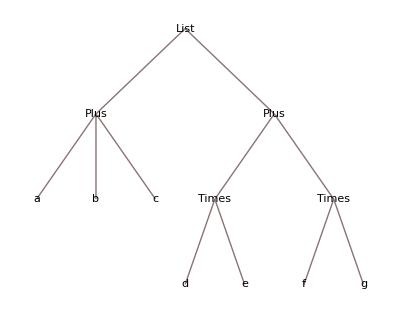

```mathematica
TreeForm[data]
```

```mathematica
Level[data,1]
```

{a+b+c,{{1,2},{3,4}}}

```mathematica
Manipulate[Level[data,{n}],{n,0,3,1}]
```

### Exercises Set 1

Which of the following general Elements are atomic?

String

Built-in Symbol

Entity

Integer

Real

List

Rational

Symbol

For the following questions consider the following 9 expressions

```mathematica
Grid[Partition[{5,{1,2},m,Select,x+3,"\"{1,2,3}\"",HoldForm[1+7],Log[7],HoldForm[Log[7.]]},3],Frame->All]
```

5 | {1,2} | m
Select | 3+x | "{1,2,3}"
1+7 | Log[7] | Log[7.]

Which expressions are atomic?

|   |  
  |   |  
  |   |

What are the heads of the expressions?

|   |  
  |   |  
  |   |

Can the second Part of an expression be a List?

Can the second argument of the function Part be a list?